```mathematica
(*css zebrafinch model*)
(*recursions for a simple oblique and individual only learning stage structured population*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs(lsI vI z +lsO qO ) + nh vh(lhI vI z +lhO qO );
NNn :=ns vs(lsI vI (1-z)+lsO(1- qO) ) + nh vh(lhI vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
(*marrix of transition probabilities between states*)
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs(lsI vI z +lsO qO ), vh(lhI vI z +lhO qO ), 0, 0}, {vs(lsI vI (1-z)+lsO(1- qO) ), vh(lhI vI (1-z)+lhO(1- qO) ), 0, 0}})
```

```mathematica
(*Solve for Qhat*)
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa]
```

{{Fa→(-bn lhO u vh+bn lhO pn u vh-bn lhI vh vI+bn lhI pn vh vI-bn lsO pn u vs-bn lsI pn vI vs+ba lhI vh vI z-bn lhI vh vI z-ba lhI pa vh vI z+bn lhI pn vh vI z+ba lsI pa vI vs z-bn lsI pn vI vs z-√(-4 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs) (-bn lhI vh vI z+bn lhI pn vh vI z-bn lsI pn vI vs z)+(bn lhO u vh-bn lhO pn u vh+bn lhI vh vI-bn lhI pn vh vI+bn lsO pn u vs+bn lsI pn vI vs-ba lhI vh vI z+bn lhI vh vI z+ba lhI pa vh vI z-bn lhI pn vh vI z-ba lsI pa vI vs z+bn lsI pn vI vs z)^2))/(2 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs))},{Fa→(-bn lhO u vh+bn lhO pn u vh-bn lhI vh vI+bn lhI pn vh vI-bn lsO pn u vs-bn lsI pn vI vs+ba lhI vh vI z-bn lhI vh vI z-ba lhI pa vh vI z+bn lhI pn vh vI z+ba lsI pa vI vs z-bn lsI pn vI vs z+√(-4 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs) (-bn lhI vh vI z+bn lhI pn vh vI z-bn lsI pn vI vs z)+(bn lhO u vh-bn lhO pn u vh+bn lhI vh vI-bn lhI pn vh vI+bn lsO pn u vs+bn lsI pn vI vs-ba lhI vh vI z+bn lhI vh vI z+ba lhI pa vh vI z-bn lhI pn vh vI z-ba lsI pa vI vs z+bn lsI pn vI vs z)^2))/(2 (ba lhO u vh-bn lhO u vh-ba lhO pa u vh+bn lhO pn u vh+ba lhI vh vI-bn lhI vh vI-ba lhI pa vh vI+bn lhI pn vh vI+ba lsO pa u vs-bn lsO pn u vs+ba lsI pa vI vs-bn lsI pn vI vs))}}

```mathematica
subtest = {ba->3,bn->1,z->0.6,pa->0.01,pn->0.99,vs->0.8,vh->0.95,vI->0.7  ,lsO-> 0.2 ,lsI-> 0.8,lhO-> 0.2,lhI-> 0.8 ,u-> 0.1 };
```

```mathematica
Fasols[[2,1,2]]/.subtest (*check it is stable qhat with values, select positive q-hat*)
 Fasols[[2,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI}/.{pa->0,pn->1}(*copy and past solution below*)
```

0.57931

(-bn LSO u vs-bn LSI vI vs+ba LHI vh vI z-bn LSI vI vs z+√(4 bn LSI vI vs (ba LHO u vh+ba LHI vh vI-bn LSO u vs-bn LSI vI vs) z+(bn LSO u vs+bn LSI vI vs-ba LHI vh vI z+bn LSI vI vs z)^2))/(2 (ba LHO u vh+ba LHI vh vI-bn LSO u vs-bn LSI vI vs))

```mathematica
QHAT[LHI_,LHO_,LSO_,LSI_] := (-bn LSO u vs-bn LSI vI vs+ba LHI vh vI z-bn LSI vI vs z+√(4 bn LSI vI vs (ba LHO u vh+ba LHI vh vI-bn LSO u vs-bn LSI vI vs) z+(bn LSO u vs+bn LSI vI vs-ba LHI vh vI z+bn LSI vI vs z)^2))/(2 (ba LHO u vh+ba LHI vh vI-bn LSO u vs-bn LSI vI vs));
```

```mathematica
(*substitute solution for Qhat into matrix*)
AA2=AA/.{Na->Qh,Nn->(1-Qh)}
```

{{0,0,ba pa,bn pn},{0,0,ba (1-pa),bn (1-pn)},{vs (lsO Qh (1-u)+lsI vI z),vh (lhO Qh (1-u)+lhI vI z),0,0},{vs (lsO (1-Qh (1-u))+lsI vI (1-z)),vh (lhO (1-Qh (1-u))+lhI vI (1-z)),0,0}}

```mathematica
(*AA3=AA2/.{Qh->Qhat};*)
AA3=AA2;
```

```mathematica
AA4=AA3/.{pa->0,pn->1}; (*make cues 100% reliable to simplify solution*)
```

```mathematica
(*calculate eigenvalues of system after subbing in Qhat*)
LL=Eigenvalues[AA4]
```

{-√(1/2 ba lhO Qh vh-1/2 ba lhO Qh u vh+(bn lsO vs)/2-1/2 bn lsO Qh vs+1/2 bn lsO Qh u vs+1/2 bn lsI vI vs+1/2 ba lhI vh vI z-1/2 bn lsI vI vs z-1/2 √((-ba lhO Qh vh+ba lhO Qh u vh-bn lsO vs+bn lsO Qh vs-bn lsO Qh u vs-bn lsI vI vs-ba lhI vh vI z+bn lsI vI vs z)^2-4 (ba bn lhO lsI Qh vh vI vs-ba bn lhI lsO Qh vh vI vs-ba bn lhO lsI Qh u vh vI vs+ba bn lhI lsO Qh u vh vI vs-ba bn lhO lsI vh vI vs z+ba bn lhI lsO vh vI vs z))),√(1/2 ba lhO Qh vh-1/2 ba lhO Qh u vh+(bn lsO vs)/2-1/2 bn lsO Qh vs+1/2 bn lsO Qh u vs+1/2 bn lsI vI vs+1/2 ba lhI vh vI z-1/2 bn lsI vI vs z-1/2 √((-ba lhO Qh vh+ba lhO Qh u vh-bn lsO vs+bn lsO Qh vs-bn lsO Qh u vs-bn lsI vI vs-ba lhI vh vI z+bn lsI vI vs z)^2-4 (ba bn lhO lsI Qh vh vI vs-ba bn lhI lsO Qh vh vI vs-ba bn lhO lsI Qh u vh vI vs+ba bn lhI lsO Qh u vh vI vs-ba bn lhO lsI vh vI vs z+ba bn lhI lsO vh vI vs z))),-√(1/2 ba lhO Qh vh-1/2 ba lhO Qh u vh+(bn lsO vs)/2-1/2 bn lsO Qh vs+1/2 bn lsO Qh u vs+1/2 bn lsI vI vs+1/2 ba lhI vh vI z-1/2 bn lsI vI vs z+1/2 √((-ba lhO Qh vh+ba lhO Qh u vh-bn lsO vs+bn lsO Qh vs-bn lsO Qh u vs-bn lsI vI vs-ba lhI vh vI z+bn lsI vI vs z)^2-4 (ba bn lhO lsI Qh vh vI vs-ba bn lhI lsO Qh vh vI vs-ba bn lhO lsI Qh u vh vI vs+ba bn lhI lsO Qh u vh vI vs-ba bn lhO lsI vh vI vs z+ba bn lhI lsO vh vI vs z))),√(1/2 ba lhO Qh vh-1/2 ba lhO Qh u vh+(bn lsO vs)/2-1/2 bn lsO Qh vs+1/2 bn lsO Qh u vs+1/2 bn lsI vI vs+1/2 ba lhI vh vI z-1/2 bn lsI vI vs z+1/2 √((-ba lhO Qh vh+ba lhO Qh u vh-bn lsO vs+bn lsO Qh vs-bn lsO Qh u vs-bn lsI vI vs-ba lhI vh vI z+bn lsI vI vs z)^2-4 (ba bn lhO lsI Qh vh vI vs-ba bn lhI lsO Qh vh vI vs-ba bn lhO lsI Qh u vh vI vs+ba bn lhI lsO Qh u vh vI vs-ba bn lhO lsI vh vI vs z+ba bn lhI lsO vh vI vs z)))}

```mathematica
(*find positive, real dominant eigenvalue and set to lambda*)
LL/.subtest /. Qh -> 0.5
```

{-8.33×10^-9,8.33×10^-9,-1.21709,1.21709}

```mathematica
Simplify[LL[[4]]]
```

1/(√2)(√(ba lhO Qh vh-ba lhO Qh u vh+bn lsO vs-bn lsO Qh vs+bn lsO Qh u vs+bn lsI vI vs+ba lhI vh vI z-bn lsI vI vs z+√(4 ba bn (lhO lsI-lhI lsO) vh vI vs (Qh (-1+u)+z)+(bn vs (lsO+lsO Qh (-1+u)-lsI vI (-1+z))+ba vh (lhO (Qh-Qh u)+lhI vI z))^2)))

```mathematica
Lambda1[lsI_, lhI_, lsO_, lhO_,LHI_,LHO_,LSO_,LSI_]:= 1/(√2)(√(ba lhO QHAT[LHI,LHO,LSO,LSI] vh-ba lhO QHAT[LHI,LHO,LSO,LSI] u vh+bn lsO vs-bn lsO QHAT[LHI,LHO,LSO,LSI] vs+bn lsO QHAT[LHI,LHO,LSO,LSI] u vs+bn lsI vI vs+ba lhI vh vI z-bn lsI vI vs z+√(4 ba bn (lhO lsI-lhI lsO) vh vI vs (QHAT[LHI,LHO,LSO,LSI] (-1+u)+z)+(bn vs (lsO+lsO QHAT[LHI,LHO,LSO,LSI] (-1+u)-lsI vI (-1+z))+ba vh (lhO (QHAT[LHI,LHO,LSO,LSI]-QHAT[LHI,LHO,LSO,LSI] u)+lhI vI z))^2)));
```

```mathematica
(*solve a system of ODEs to calculate selection gradient, Richard please check to see if this is ok*)
DlsI=D[Lambda1[lsI, lhI, lsO, lhO,LHI,LHO,LSO,LSI],lsI]/. {LHI-> lhI,LHO -> lhO, LSI-> lsI, LSO-> lsO};
```

```mathematica
DlhI=D[Lambda1[lsI, lhI, lsO, lhO,LHI,LHO,LSO,LSI],lhI]/. {LHI-> lhI,LHO -> lhO, LSI-> lsI, LSO-> lsO};
```

```mathematica
DlsO=D[Lambda1[lsI, lhI, lsO, lhO,LHI,LHO,LSO,LSI],lsO]/. {LHI-> lhI,LHO -> lhO, LSI-> lsI, LSO-> lsO};
```

```mathematica
DlhO=D[Lambda1[lsI, lhI, lsO, lhO,LHI,LHO,LSO,LSI],lhO]/. {LHI-> lhI,LHO -> lhO, LSI-> lsI, LSO-> lsO};
```

```mathematica
(*initial starting conditions and number of iterations*)
lsIstart=0.9; 
lhIstart=0.9;
lsOstart=1-lsIstart;
lhOstart=1-lhIstart;
imax=500;
delta=0.01;
sub2={ba->3,bn->1,z->0.5,vs->0.8,vh->0.9,vI->0.2  ,u->0.05};
(*empty vectors to store values*)
lsItab=lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsItab=Table[0,{i,imax}];
DlhItab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
(*and setting initial vector*)
lsItab[[1]]=lsIstart;
lsOtab[[1]]=lsOstart;
lhItab[[1]]=lhIstart;
lhOtab[[1]]=lhOstart;
DlsItab[[1]]=DlsI/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlhItab[[1]]=DlhI/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlsOtab[[1]]=DlsO/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
```

```mathematica
(* below is grahing code for numerical solution with above conditions. I added delta times each derivative, starts at 2*)
For[i=2,i<imax,i++,{
lsItab[[i]]=lsItab[[i-1]]+ delta DlsI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsItab[[i]]=If[lsItab[[i]]>1,1,lsItab[[i]]];
lsItab[[i]]=If[lsItab[[i]]<0,0,lsItab[[i]]];

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhItab[[i]]=lhItab[[i-1]] + delta DlhI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhItab[[i]]=If[lhItab[[i]]>1,1,lhItab[[i]]];
lhItab[[i]]=If[lhItab[[i]]<0,0,lhItab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsItab[[i]]=DlsI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhItab[[i]]=DlhI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlsOtab[[i]]=DlsO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];
```

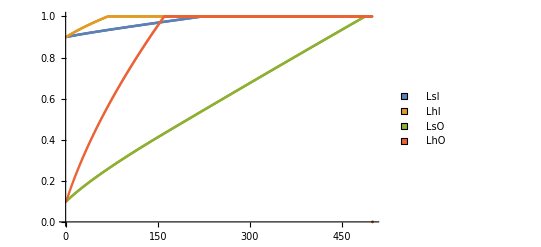

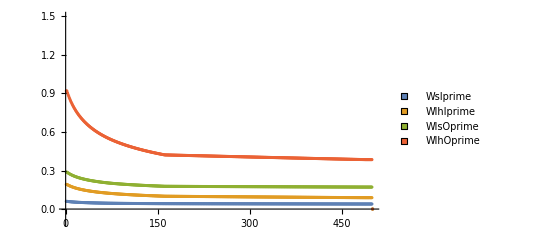

```mathematica
ListPlot[{lsItab,lhItab,lsOtab,lhOtab},PlotRange->{All,{0,1}}, PlotLegends->PointLegend[{LsI,LhI,LsO,LhO},LegendMarkers->Graphics[Rectangle[]]]]
ListPlot[{DlsItab,DlhItab,DlsOtab,DlhOtab},PlotRange->{All,{-.1,1.5}}, PlotLegends->PointLegend[{WsIprime,WlhIprime,WlsOprime,WlhOprime},LegendMarkers->Graphics[Rectangle[]]]  ]
```

```mathematica
lsItab + lsOtab+lhItab +lhOtab;
```

```mathematica
(*inverse invasion of IL*)

(* comment everything below out
lsIstart=0.1;
lhIstart=0.1;
lsOstart=0.9;
lhOstart=0.9;
imax=500;
lsItab=lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsItab=Table[0,{i,imax}];
DlhItab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.01;
sub2={ba->2,bn->1,z->0.8,vs->0.6,vh->0.9,vI->0.7  ,u->0.15};
lsItab[[1]]=lsIstart;
lsOtab[[1]]=lsOstart;
lhItab[[1]]=lhIstart;
lhOtab[[1]]=lhOstart;
DlsItab[[1]]=DlsI/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlhItab[[1]]=DlhI/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlsOtab[[1]]=DlsO/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.sub2/.{lsI->lsIstart,lhI->lhIstart,lsO->lsOstart,lhO->lhOstart};
*)
```

```mathematica
(*For[i=2,i<imax,i++,{
lsItab[[i]]=lsItab[[i-1]]+ delta DlsI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsItab[[i]]=If[lsItab[[i]]>1,1,lsItab[[i]]];
lsItab[[i]]=If[lsItab[[i]]<0,0,lsItab[[i]]];

lsOtab[[i]]=lsOtab[[i-1]]  - delta DlsO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhItab[[i]]=lhItab[[i-1]] + delta DlhI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhItab[[i]]=If[lhItab[[i]]>1,1,lhItab[[i]]];
lhItab[[i]]=If[lhItab[[i]]<0,0,lhItab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  - delta DlhO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsItab[[i]]=DlsI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhItab[[i]]=DlhI/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlsOtab[[i]]=DlsO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.sub2/.{lsI->lsItab[[i-1]],lhI->lhItab[[i-1]],lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};*)
}];
```

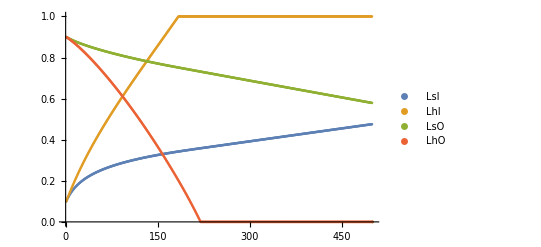

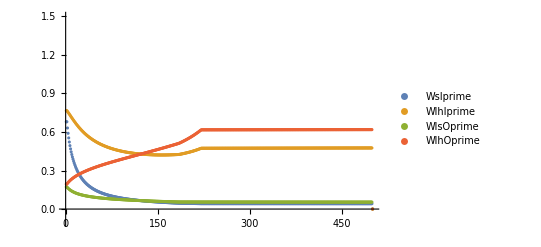

```mathematica
(*ListPlot[{lsItab,lhItab,lsOtab,lhOtab},PlotRange->{All,{0,1}}, PlotLegends->{LsI,LhI,LsO,LhO}]
ListPlot[{DlsItab,DlhItab,DlsOtab,DlhOtab},PlotRange->{All,{-.1,1.5}}, PlotLegends->{WsIprime,WlhIprime,WlsOprime,WlhOprime}]*)
```